# MAST90053 EXPERIMENTAL MATHEMATICS

## LECTURER: DR ANDREA BEDINI 2014, SEMESTER 1, WEEK 1

## Getting started

Difference between = and :=

```mathematica
Clear[x,y,f]
```

```mathematica
y=3;
```

```mathematica
f[x_]=x+y(*Evaluated the rhs to x+3*)
```

3+x

```mathematica
f[3]
```

6

```mathematica
y=1; (* change y *)
f[3] (* result doens't change *)
```

6

```mathematica
?f
```

Global`f

f[x_]=3+x

```mathematica
Clear[x,y,f]
```

```mathematica
y=3;
```

```mathematica
f[x_]:=x+y (*Leaves the rhs unevaluated*)
```

```mathematica
f[3]
```

6

```mathematica
y=1; (* change y *)
f[3] (* result changes *)
```

4

```mathematica
?f
```

Global`f

f[x_]:=x+y

Many ways of applying a function

```mathematica
Clear[f]
```

```mathematica
f[x]
```

f[x]

```mathematica
x//f
```

f[x]

```mathematica
f@x
```

f[x]

Also

```mathematica
x~f~y
```

f[x,y]

Applying a function to a list

```mathematica
f/@{1,2,3}
```

{f[1],f[2],f[3]}

Creating an array of symbols

```mathematica
Array[a,3]
```

{a[1],a[2],a[3]}

```mathematica
Array[a,{3,3}]
```

{{a[1,1],a[1,2],a[1,3]},{a[2,1],a[2,2],a[2,3]},{a[3,1],a[3,2],a[3,3]}}

## Exercise 1.

```mathematica
Clear[a,b];
a[0]=N[1,200];
b[0]=N[Sqrt[2],200];

a[n_]:=a[n]=(a[n-1]+b[n-1])/2;
b[n_]:=b[n]=Sqrt[a[n-1]b[n-1]];

a[100]//Timing
```

{0.003,1.1981402347355922074399224922803238782272126632156515582636749529464052141439156708358855564897933893759072250972437622759288775397035280307656021697649672783870543041718873877355629063532093911521661}

We actually don' t need many terms because the convergence is very fast. The following shows that we have 200 digits of the limit in just 8 iterations.

```mathematica
Table[a[n],{n,0,10}]//TableForm
```

1.
1.2071067811865475244008443621048490392848359376884740365883398689953662392310535194251937671638207863675069231154561485124624180279253686063220607485499679157066113329637527963778999752505763910302857
1.1981569480946342955591721663326624772889040150761457248036710468574164537289853396479875558509792300417721589451126808492630721948576081815537108055439928453883814221836549443255311590597331576028659
1.1981402347938772090828788690764074639904586267422005612960300874695187288965656017172107528031629559988999240908327376931371883308932910282490346917312721964152682785841559424611110635303780135667204
1.1981402347355922074406313286331040863611447412997045000859512326994922004302814859237238787583078845144900646163753229438234206266282505698336242658092910252953057984753532225839753084117802606870809
1.1981402347355922074399224922803238782272127680550018396664700623630439649400594480578057826297755770510541250711912055564658475224856218821522842195158327840109690058586758030726458227364631411950619
1.1981402347355922074399224922803238782272126632156515582636749529464052141439156708358878498960760546622258729593801194030659859170842093036649098656631624363355480019205726780631644614928842959412897
1.1981402347355922074399224922803238782272126632156515582636749529464052141439156708358855564897933893759072250972437622759288775397035280307656021697649672783870543041718873888330371887625072850433427
1.1981402347355922074399224922803238782272126632156515582636749529464052141439156708358855564897933893759072250972437622759288775397035280307656021697649672783870543041718873877355629063532093911521661
1.1981402347355922074399224922803238782272126632156515582636749529464052141439156708358855564897933893759072250972437622759288775397035280307656021697649672783870543041718873877355629063532093911521661
1.1981402347355922074399224922803238782272126632156515582636749529464052141439156708358855564897933893759072250972437622759288775397035280307656021697649672783870543041718873877355629063532093911521661

```mathematica
i1=a[10]
i2=b[10]
```

1.1981402347355922074399224922803238782272126632156515582636749529464052141439156708358855564897933893759072250972437622759288775397035280307656021697649672783870543041718873877355629063532093911521661

1.1981402347355922074399224922803238782272126632156515582636749529464052141439156708358855564897933893759072250972437622759288775397035280307656021697649672783870543041718873877355629063532093911521661

Version without the trick is exponentally slower

```mathematica
Clear[a,b];
a[0]=N[1,200];
b[0]=N[Sqrt[2],200];

a[n_]:=(a[n-1]+b[n-1])/2;
b[n_]:=Sqrt[a[n-1]b[n-1]];

a[15]//Timing
```

{0.29195,1.1981402347355922074399224922803238782272126632156515582636749529464052141439156708358855564897933893759072250972437622759288775397035280307656021697649672783870543041718873877355629063532093911521661}

## Exercise 2.

```mathematica
i3=2/π NIntegrate[1/(√(1-t^4)),{t,0,1},AccuracyGoal->100,WorkingPrecision->200]
Precision[i3]
1/i3
```

0.83462684167407318628142973279904680899399301349034700244982737010368199270952641186969116035127532412906785035241201008672478530365275881501365946644000656053712962252290781666120215009545904972790532

200.

1.1981402347355922074399224922803238782272126632156515582636749529464052141439156708358855564897933893759072250972437622759288828569179180494718583185021765392079708112570913297630099487488237651078555

```mathematica
i2 i3-1
```

-4.4378898528452463794977355138030374548702742521642567146182149798048143001×10^-126

## Exercise 3.

```mathematica
L[0]=1;
L[n_]:=L[n-1]+n;
```

```mathematica
Table[L[n],{n,20}]
```

{2,4,7,11,16,22,29,37,46,56,67,79,92,106,121,137,154,172,191,211}

```mathematica
Table[n(n+1)/2+1,{n,20}]
```

{2,4,7,11,16,22,29,37,46,56,67,79,92,106,121,137,154,172,191,211}

```mathematica
Hyperlink["Check on the On-Line Encyclopedia of Integer Sequences","https://oeis.org/A000124"]
```

## Exercise 4.

```mathematica
Table[Binomial[n,m]~Mod~2,{n,0,2^8},{m,0,2^8}]//Image//ColorNegate
```

-Graphics-

PS: There are many other ways.

## Exercise 5.

```mathematica
Clear[a,x,y];
a[x_,y_,0]=x;
a[x_,y_,n_]:=a[x,y,n]=1/2(a[x,y,n-1]^2+y^2);
Flatten[Table[{x,y,a[x,y,n]},{n,4},{x,-2,2,.1},{y,-2,2,.1}],2]//ListPointPlot3D
```

-Graphics3D-

Here is slightly different version (but it doesn’t show the x and y axes).

```mathematica
Clear[a,x,y];
a[x_,y_,0]=x;
a[x_,y_,n_]:=a[x,y,n]=1/2(a[x,y,n-1]^2+y^2);
Table[a[x,y,n],{n,4},{x,-2,2,.1},{y,-2,2,.1}]//ListPointPlot3D
```

-Graphics3D-

## Exercise 6.

```mathematica
A={{3/2,1/2},{-1/2,1/2}}
MatrixForm/@Table[MatrixPower[A,n],{n,6}]
```

{{3/2,1/2},{-1/2,1/2}}

{(3/2 | 1/2
-1/2 | 1/2),(2 | 1
-1 | 0),(5/2 | 3/2
-3/2 | -1/2),(3 | 2
-2 | -1),(7/2 | 5/2
-5/2 | -3/2),(4 | 3
-3 | -2)}

```mathematica
MatrixForm/@Table[{{n/2+1,n/2},{-n/2,-n/2+1}},{n,6}]
```

{(3/2 | 1/2
-1/2 | 1/2),(2 | 1
-1 | 0),(5/2 | 3/2
-3/2 | -1/2),(3 | 2
-2 | -1),(7/2 | 5/2
-5/2 | -3/2),(4 | 3
-3 | -2)}

## Exercise 7.

```mathematica
A=({{2, -1, 0}, {-1, 2, -1}, {0, -1, -2}});
MatrixForm[A]
```

(2 | -1 | 0
-1 | 2 | -1
0 | -1 | -2)

Define a matrix of unknowns B. Any undefined symbol will work as an unknown, here I am using some fancy formatting.

```mathematica
B=Array[Subscript[b, ##]&,{3,3}];
MatrixForm[B]
```

(b_(1,1) | b_(1,2) | b_(1,3)
b_(2,1) | b_(2,2) | b_(2,3)
b_(3,1) | b_(3,2) | b_(3,3))

I want to show that for each B that commutes with A I can find α, β and γ such that B == α A.A + β A + γ IdentityMatrix[3]

Use the commutation relation to reduce the number of unknowns in B

```mathematica
B/.Solve[A.B-B.A==0]//First
MatrixForm[%]
```

{{-4 b_(3,2)+b_(3,3),-4 b_(3,1)+b_(3,2),b_(3,1)},{-4 b_(3,1)+b_(3,2),b_(3,1)-4 b_(3,2)+b_(3,3),b_(3,2)},{b_(3,1),b_(3,2),b_(3,3)}}

(-4 b_(3,2)+b_(3,3) | -4 b_(3,1)+b_(3,2) | b_(3,1)
-4 b_(3,1)+b_(3,2) | b_(3,1)-4 b_(3,2)+b_(3,3) | b_(3,2)
b_(3,1) | b_(3,2) | b_(3,3))

Find α, β and γ

```mathematica
Solve[%==α A.A+β A+γ IdentityMatrix[3],{α,β,γ}]//First
```

{α→b_(3,1),β→-b_(3,2),γ→-5 b_(3,1)-2 b_(3,2)+b_(3,3)}

## Exercise 8.

```mathematica
Clear[A]
A[n_]:=Sum[Fibonacci[n-k] 10^k,{k,0,n}]
```

```mathematica
Table[A[n],{n,10}]
```

{1,11,112,1123,11235,112358,1123593,11235951,112359544,1123595495}

We can find a closed formula using Binet' s formula

```mathematica
ϕ=(1+√5)/2;
Sum[(ϕ^(n-k)-(-ϕ)^(-n+k))/(√5)10^k,{k,0,n}]//FullSimplify
Table[%,{n,10}]//FullSimplify
```

((-1-√5)^(-1-n) ((-3-√5)^n (31+11 √5)-2^n (-19+√5+2 5^(1+n) (-1-√5)^n (5+√5))))/(89 √5)

{1,11,112,1123,11235,112358,1123593,11235951,112359544,1123595495}

## Exercise 9.

If you understand this you are a Mathematica wizard

```mathematica
Clear[a,t,ℐ]
$Assumptions=a>0&&t>0;
ℐ[a_,t_]=∫_-t^∞ a^x/Gamma[x+1] ⅆx+∫_0^∞ (E^(-a x)x^(t-1))/(π^2+Log[x]^2)(Cos[π t]-Sin[π t]/π Log[x])ⅆx//Hold
```

Hold[∫_-t^∞ a^x/Gamma[x+1]ⅆx+∫_0^∞ ((ⅇ^(-a x) x^(t-1)) (Cos[π t]-(Sin[π t] Log[x])/π))/(π^2+Log[x]^2)ⅆx]

```mathematica
Block[{Integrate},D[ℐ[a,t],t]//ReleaseHold]
```

a^-t/Gamma[1-t]-(a^-t Gamma[t] Sin[π t])/π

```mathematica
%//FullSimplify
```

0

```mathematica
Block[{Integrate},ℐ[a,0]//ReleaseHold//Evaluate//Hold]
```

Hold[∫_0^∞ a^x/Gamma[1+x]ⅆx+∫_0^∞ ⅇ^(-a x)/(x (π^2+Log[x]^2))ⅆx]

```mathematica
Block[{Integrate},D[%,a]//ReleaseHold//Evaluate//Hold]
```

Hold[∫_0^∞ (a^(-1+x) x)/Gamma[1+x]ⅆx+∫_0^∞ -ⅇ^(-a x)/(π^2+Log[x]^2)ⅆx]

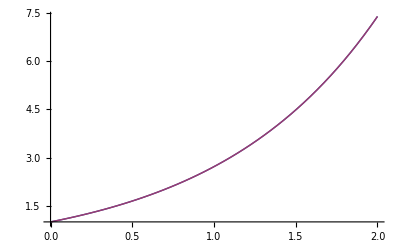

```mathematica
Plot[{%//N//ReleaseHold,Exp[a]},{a,0,2}]
```

```mathematica
Block[{Integrate},D[ℐ[a,0],a]//ReleaseHold//FullSimplify//Evaluate//Hold]
Block[{Integrate},D[ℐ[a,0],{a,2}]//ReleaseHold//FullSimplify//Evaluate//Hold]
Block[{Integrate},D[ℐ[a,0],{a,3}]//ReleaseHold//FullSimplify//Evaluate//Hold]
```

Hold[∫_0^∞ a^(-1+x)/Gamma[x]ⅆx+∫_0^∞ -ⅇ^(-a x)/(π^2+Log[x]^2)ⅆx]

Hold[∫_0^∞ a^(-2+x)/Gamma[-1+x]ⅆx+∫_0^∞ (ⅇ^(-a x) x)/(π^2+Log[x]^2)ⅆx]

Hold[∫_0^∞ a^(-3+x)/Gamma[-2+x]ⅆx+∫_0^∞ -(ⅇ^(-a x) x^2)/(π^2+Log[x]^2)ⅆx]